```mathematica
Guy F. Mongelli
Assigment 1: Additional Notes
```

Guy F.Mongelli

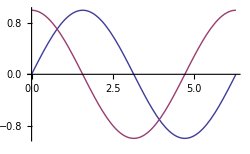

```mathematica
Plot[{Sin[x],Cos[x]},{x,0,2*Pi}]
```

```mathematica
Sin[Pi/4]
```

1/(√2)

```mathematica
Cos[Pi/4]
```

1/(√2)

```mathematica
Log[0]
```

-∞

```mathematica
Log[1]
```

0

```mathematica
Log[-1]
```

ⅈ π

```mathematica
Log[1+ⅈ]
```

Log[1+ⅈ]

```mathematica
Problem 1:
```

```mathematica
Looking at the inversion matrix:
```

```mathematica
MatrixForm[FullSimplify[Inverse[({{Cos[ϕ] Sin[θ], r Cos[θ] Cos[ϕ], -r Sin[θ] Sin[ϕ]}, {Sin[θ] Sin[ϕ], r Cos[θ] Sin[ϕ], r Cos[ϕ] Sin[θ]}, {Cos[θ], -r Sin[θ], 0}})]]]
```

((√(1-z^2/(x^2+y^2)))/(√(1+y^2/x^2)) | (y √(1-z^2/(x^2+y^2)))/(x √(1+y^2/x^2)) | z/(√(x^2+y^2))
z/((x^2+y^2) √(1+y^2/x^2)) | (x y √(1+y^2/x^2) z)/((x^2+y^2)^2) | -(√(1-z^2/(x^2+y^2)))/(√(x^2+y^2))
-y/(x √(x^2+y^2) √(1+y^2/x^2) √(1-z^2/(x^2+y^2))) | 1/(√(x^2+y^2) √(1+y^2/x^2) √(1-z^2/(x^2+y^2))) | 0)

```mathematica
MatrixForm[FullSimplify[Det[Inverse[({{Cos[ϕ] Sin[θ], r Cos[θ] Cos[ϕ], -r Sin[θ] Sin[ϕ]}, {Sin[θ] Sin[ϕ], r Cos[θ] Sin[ϕ], r Cos[ϕ] Sin[θ]}, {Cos[θ], -r Sin[θ], 0}})]]]]
```

1/((x^2+y^2) √(1-z^2/(x^2+y^2)))

```mathematica
Then, this matrix should be simplified based upon the definitions of r, θ, ϕ in terms of x,y,and z to describe the transformation from Carthesian to spherical coordinates.
```

```mathematica
r=√(x^2+y^2)
θ=ArcCos[z/r]
ϕ=ArcTan[y/x]
```

√(x^2+y^2)

ArcCos[z/(√(x^2+y^2))]

ArcTan[y/x]

```mathematica
MatrixForm[FullSimplify[Inverse[({{Cos[ϕ] Sin[θ], r Cos[θ] Cos[ϕ], -r Sin[θ] Sin[ϕ]}, {Sin[θ] Sin[ϕ], r Cos[θ] Sin[ϕ], r Cos[ϕ] Sin[θ]}, {Cos[θ], -r Sin[θ], 0}})]]]
```

((√(1-z^2/(x^2+y^2)))/(√(1+y^2/x^2)) | (y √(1-z^2/(x^2+y^2)))/(x √(1+y^2/x^2)) | z/(√(x^2+y^2))
z/((x^2+y^2) √(1+y^2/x^2)) | (x y √(1+y^2/x^2) z)/((x^2+y^2)^2) | -(√(1-z^2/(x^2+y^2)))/(√(x^2+y^2))
-y/(x √(x^2+y^2) √(1+y^2/x^2) √(1-z^2/(x^2+y^2))) | 1/(√(x^2+y^2) √(1+y^2/x^2) √(1-z^2/(x^2+y^2))) | 0)

```mathematica
For pure curiosity, calculate the determinant of this inverse matrix.
```

```mathematica
MatrixForm[FullSimplify[Det[Inverse[({{Cos[ϕ] Sin[θ], r Cos[θ] Cos[ϕ], -r Sin[θ] Sin[ϕ]}, {Sin[θ] Sin[ϕ], r Cos[θ] Sin[ϕ], r Cos[ϕ] Sin[θ]}, {Cos[θ], -r Sin[θ], 0}})]]]]
```

1/((x^2+y^2) √(1-z^2/(x^2+y^2)))

```mathematica
Clear[r,θ,ϕ]
```

```mathematica
JacobianMatrix[{x, y, z},Cylindrical]//MatrixForm
```

(Cos[r Sin[θ] Sin[ϕ]] | -r Cos[ϕ] Sin[θ] Sin[r Sin[θ] Sin[ϕ]] | 0
Sin[r Sin[θ] Sin[ϕ]] | r Cos[ϕ] Cos[r Sin[θ] Sin[ϕ]] Sin[θ] | 0
0 | 0 | 1)

```mathematica
JacobianDeterminant[{x, y, z},Cylindrical]
```

r Cos[ϕ] Sin[θ]

```mathematica
I'd like to characterize the mappings between teh various coordinate systems.  To do this I will first define their relevant transformations from or to carthesian.
```

```mathematica
For conversion from carthesian to spherical, consider:
```

```mathematica
f=MatrixForm[({{x}, {y}, {z}})]
```

```mathematica
Problem 3:
```

```mathematica
At first, i had not read Prof. Edwards' notes and derived this, which is not completely accurate, yet here it is retained.
```

```mathematica
ComplexExpand[Log[a+ⅈ*b]]
```

ⅈ Arg[a+ⅈ b]+1/2 Log[a^2+b^2]

```mathematica
The following expansion makes use of Euler's formula:
```

```mathematica
ComplexExpand[Exp[a+ⅈ*b]]
```

ⅇ^a Cos[b]+ⅈ ⅇ^a Sin[b]

```mathematica
If we consider the complex plane, we may substitute x for a and y for i*b, realizing that these coordinates have the same orthogonality condition.  Then these functions can be understood in terms of a 3D plot.
```

```mathematica
t[x_,y_]=Log[x+y]
```

Log[x+y]

```mathematica
s[x_,y_]=Exp[x+y]
```

ⅇ^(x+y)

```mathematica
The two methods for understanding the complex plane are (i) to fix either a or b and plot the function as it relates to the non-fixed variable or (ii) to plot a contour map.  Both or these are done here.  The domain of one system becomes the codomain of the other and visa-versa since these are inverse functions.
```

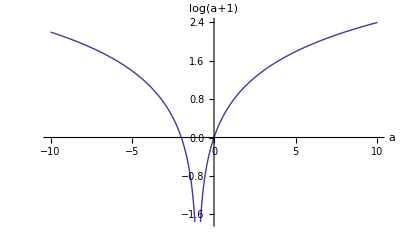

```mathematica
Plot[Re[t[x,1]],{x,-10,10},AxesLabel->{a,t[a,1]}]
```

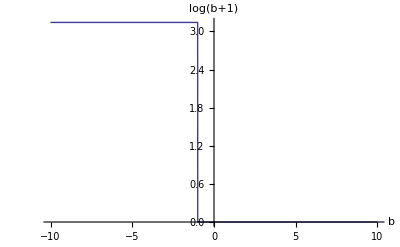

```mathematica
Plot[Im[t[1,b]],{b,-10,10},AxesLabel->{b,t[1,b]}]
```

```mathematica
Plot3D[Log[a+b],{a,-10,10},{b,-10,10},AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
Plot3D[Exp[a+b],{a,-10,10},{b,-10,10},AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
We know that these functions are inverses because compounding them returns the identity element for this function: a+b.
```

```mathematica
Plot3D[Exp[Log[a+b]],{a,-10,10},{b,-10,10},AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
The domain of the Log[z] function is .  The codomain of the Log[z] function is .  The domain of the Exp[z] is . The codomain of the Exp[z] function is.
```

```mathematica
Clear[x,y,z]
```

```mathematica
Plot3D[Exp[x]Cos[y],{x,-10,10},{y,-10,10},AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
To create the Cosh function, add the Conjugate:
```

```mathematica
Plot3D[Exp[x]Cos[y]+Exp[-x]Cos[y],{x,-10,10},{y,-10,10},AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
Plot3D[Exp[x]Sin[y],{x,-10,10},{y,-10,10},AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
To create the sinh function add the conjugate
```

```mathematica
Plot3D[Exp[x]Sin[y]+Exp[-x]Sin[y],{x,-10,10},{y,-10,10},AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
The Sinh and Cosh functions are both even in x, while the Cosh function is odd in y and Sinh is even in y.
```